## Graph

## Basic Examples

An undirected graph:



```mathematica
Graph[{1<->2,2<->3,3<->1}]
```

A directed graph:

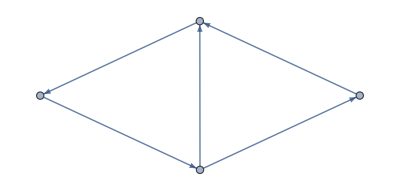

```mathematica
Graph[{1->2,2->3,3->4,4->1,2->4}]
```

Style vertexes and edges:

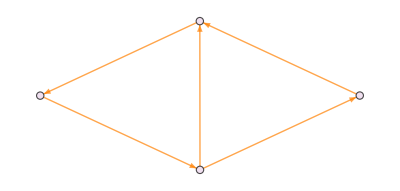

```mathematica
Graph[{1->2,2->3,3->4,4->1,2->4},VertexStyle->LightPurple,EdgeStyle->Orange]
```

Use wrappers to input directly:

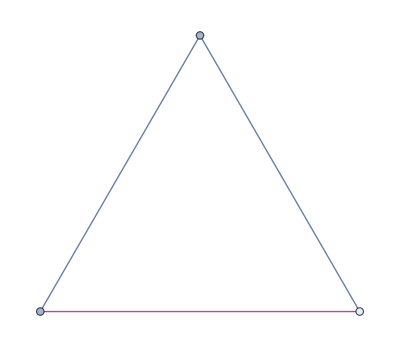

```mathematica
Graph[{1,2,Style[3,LightBlue]},{1<->2,2<->3,Style[3<->1,Purple]}]
```

Label vertices and edges:

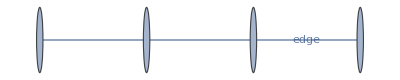

```mathematica
Graph[{1<->2,2<->3,Labeled[3<->4,"edge"]}]
```

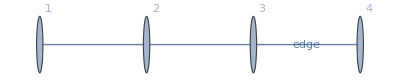

```mathematica
Graph[{1<->2,2<->3,Labeled[3<->4,"edge"]},VertexLabels->"Name"]
```

Use different vertices and edges:

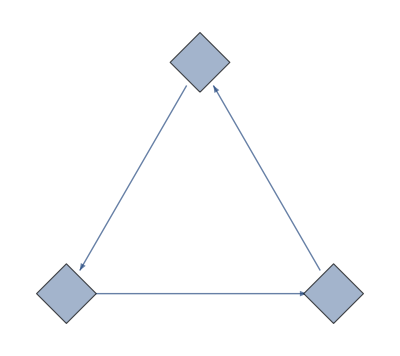

```mathematica
Graph[{1->2,2->3,3->1},VertexShapeFunction->"Diamond",VertexSize->Medium]
```

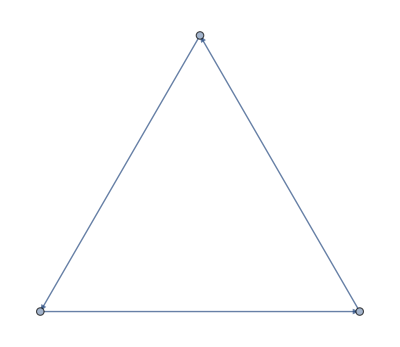

```mathematica
Graph[{1->2,2->3,3->1},EdgeShapeFunction->"CarvedArcArrow"]
```

## Options

### AnnotationRules

Specify an annotation for vertices:

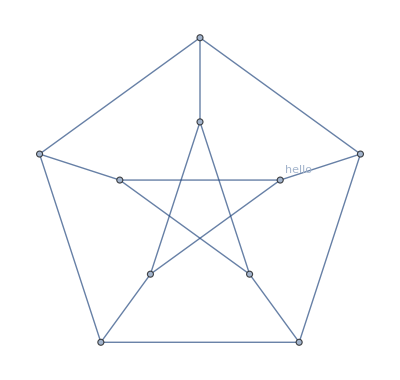

```mathematica
Graph[PetersenGraph[],AnnotationRules->{1->{VertexLabels->"hello"}}]
```

Edges:

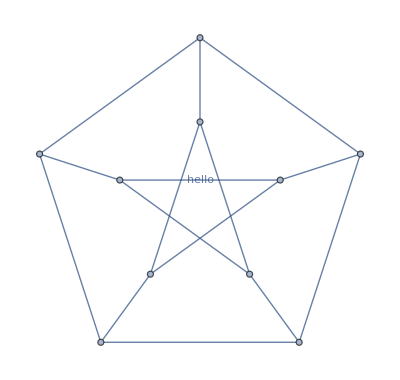

```mathematica
Graph[PetersenGraph[],AnnotationRules->{1<->4->{EdgeLabels->"hello"}}]
```

### DirectedEdges

By default, a directed graph is generated when giving a list of rules:



```mathematica
Graph[{1->2,2->3,3->1}]
```

Use DirectedEdges->False to interpret rules as undirected edges:

```mathematica
Graph[{1->2,2->3,3->1},DirectedEdges->False]
```

-Graphics-

Use DirectedEdge or UndirectedEdge to specify whether a graph is directed or not:

### EdgeLabels

```mathematica
{Graph[{1->2,2->3,3->1}],Graph[{1<->2,2<->3,3<->1}]}
```

{-Graphics-,-Graphics-}

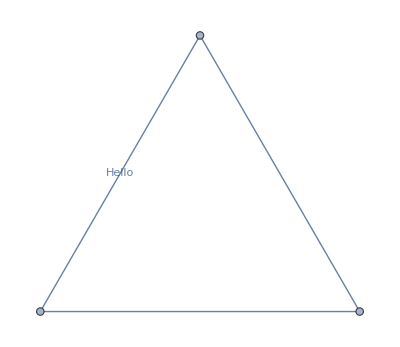

```mathematica
Graph[{1<->2,2<->3,3<->1},EdgeLabels->{1<->2->"Hello"}]
```

```mathematica
el={1<->2,2<->3,3<->1};
```

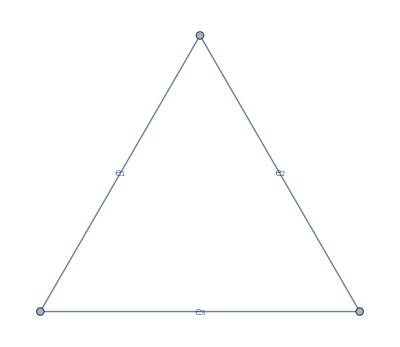

```mathematica
Graph[el,EdgeLabels->Table[el[[i]]->Subscript[e, i],{i,Length[el]}]]
```

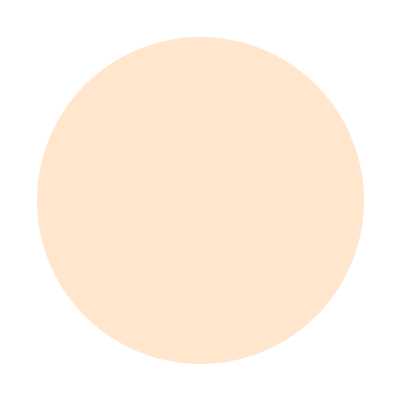
{-Graphics-,-Graphics3D-,-Graphics-}

```mathematica
edgeLabelImages=Graphics[#,ImageSize->Tiny]&/@{Graphics[{LightOrange,Disk[{3,4}]}],Graphics3D[{Torus[RandomReal[2,{3}],{1,2}]}],PolyhedronData["MathematicaPolyhedron","Image"]}
```

```mathematica
Graph[{1<->2,2<->3,3<->1},EdgeLabels->{1<->2->-Graphics-,2<->3->-Graphics3D-,3<->1->-Graphics-}]
```

-Graphics-

Use Placed with symbolic locations to control label placement along an edge:

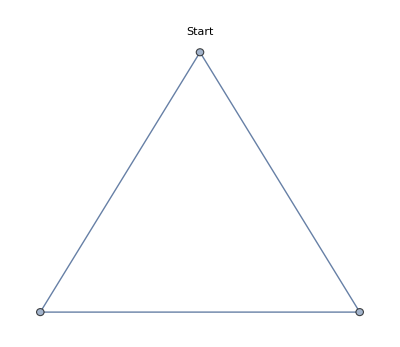
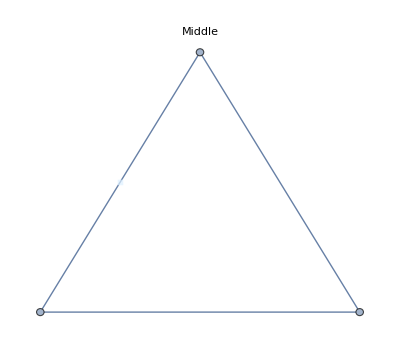
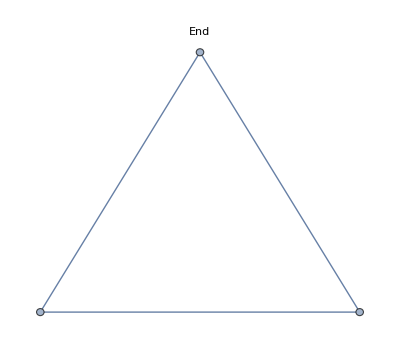

```mathematica
Table[Graph[{1<->2,2<->3,3<->1},EdgeLabels->{1<->2->Placed[-Graphics-,kp]},PlotLabel->kp],{kp,{"Start","Middle","End"}}]
```

Use explicit coordinates to place labels:

```mathematica
Graphics[{LightBlue,Rectangle[]},ImageSize->50]
```

-Graphics-

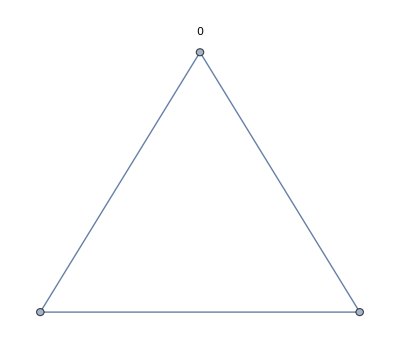
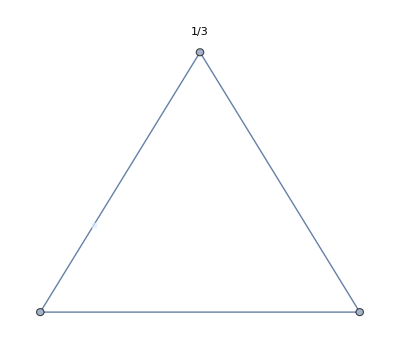
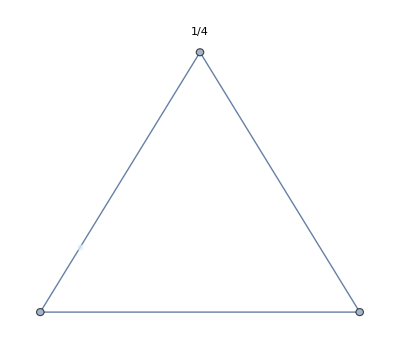

```mathematica
Table[Graph[{1<->2,2<->3,3<->1},EdgeLabels->{1<->2->Placed[-Graphics-,kp]},PlotLabel->kp,BaselinePosition->Axis],{kp,{0,1/3,1/4}}]
```

Vary positions within the label:

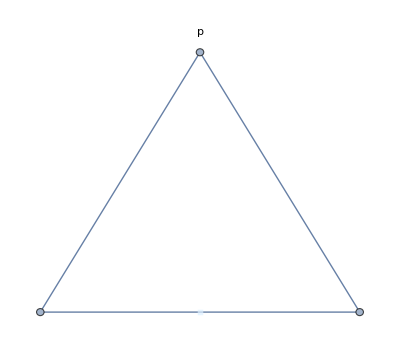
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Graph[{1<->2,2<->3,3<->1},EdgeLabels->{1<->3->Placed[-Graphics-,{1/2,kp}]},PlotLabel->p,BaselinePosition->Axis],{kp,{{0,0},{1/2,1/2},{1,1}}}]
```

Place multiple labels using Placed in a wrapper:

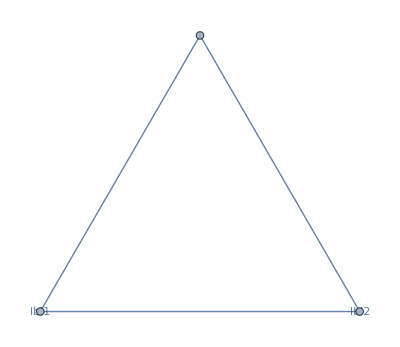

```mathematica
Graph[{1<->2,2<->3,Labeled[3<->1,Placed[{"lbl1","lbl2"},{"Start","End"}]]}]
```

Use automatic labeling by values through Tooltip and StatusArea:

```mathematica
Graph[{1<->2,2<->3,3<->1},EdgeLabels->Placed["Name",Tooltip]]
```

-Graphics-

```mathematica
Graph[{1<->2,2<->3,3<->1},EdgeLabels->Placed["Name",StatusArea]]
```

-Graphics-

### EdgeShapeFunction

Get a list of build-in settings for EdgeShapeFunction:

```mathematica
ResourceData["EdgeShapeFunction"]
```

{Arrow,BoxLine,CarvedArcArrow,CarvedArrow,DashedLine,DiamondLine,DotLine,DottedLine,FilledArcArrow,FilledArrow,HalfFilledArrow,HalfFilledDoubleArrow,HalfUnfilledArrow,HalfUnfilledDoubleArrow,Line,ShortCarvedArcArrow,ShortCarvedArrow,ShortFilledArcArrow,ShortFilledArrow,ShortUnfilledArcArrow,ShortUnfilledArrow,UnfilledArcArrow,UnfilledArrow}

Undirected edges including the basic line:

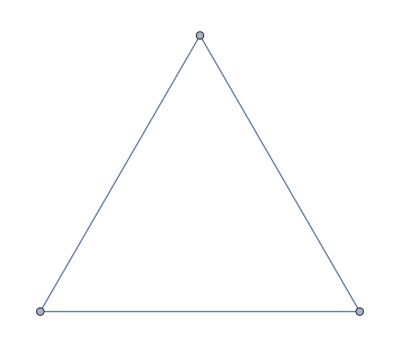

```mathematica
Graph[{1<->2,2<->3,3<->1},EdgeShapeFunction->"Line"]
```

Lines with different glyphs on the edges:

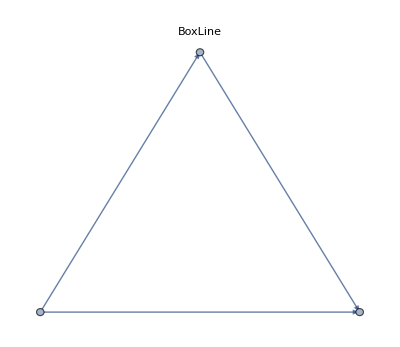
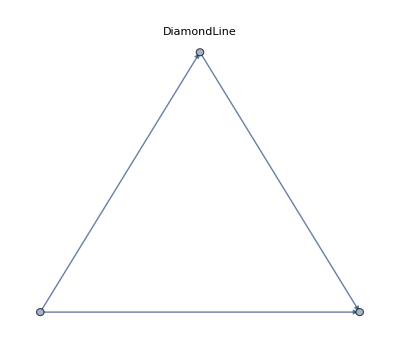
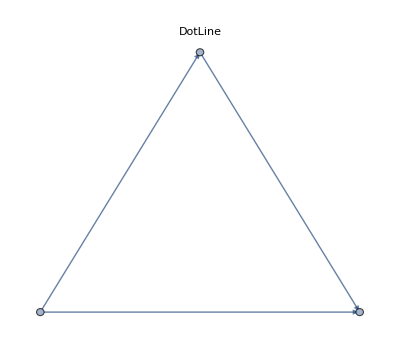

```mathematica
Table[Graph[{1<->2,2<->3,3<->1},EdgeShapeFunction->{{kef,"ArrowSize"->0.1}},PlotLabel->kef],{kef,{"BoxLine","DiamondLine","DotLine"}}]
```

Directed edges including solid arrows:

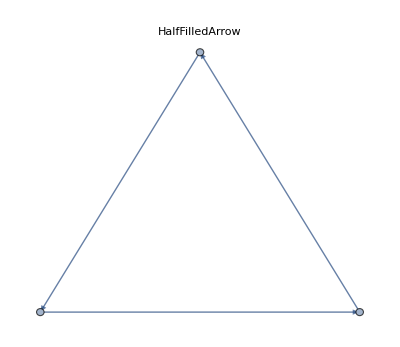
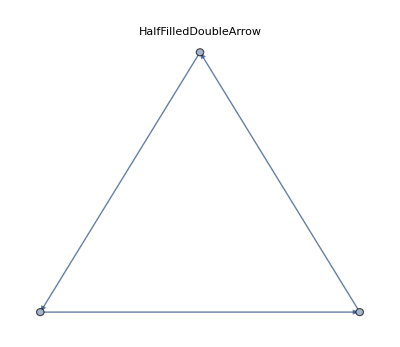
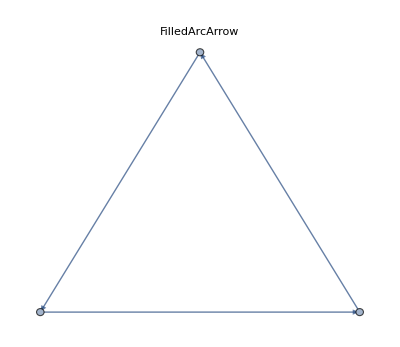
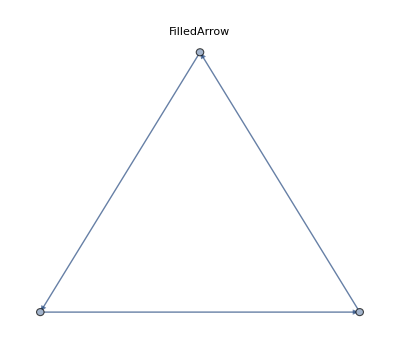
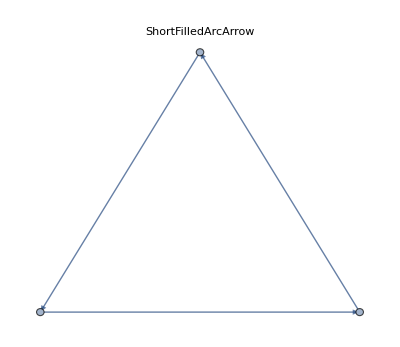
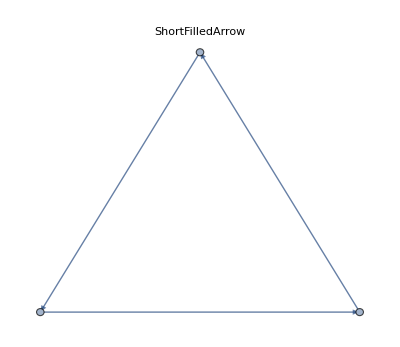

```mathematica
Table[Graph[{1->2,2->3,3->1},EdgeShapeFunction->{{kef,"ArrowSize"->0.1}},PlotLabel->Style[kef,10]],{kef,ResourceData["EdgeShapeFunction","FilledArrow"]}]
```

Line arrows:

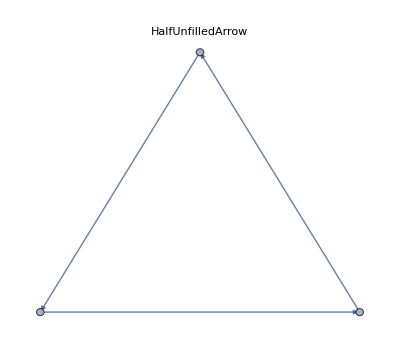
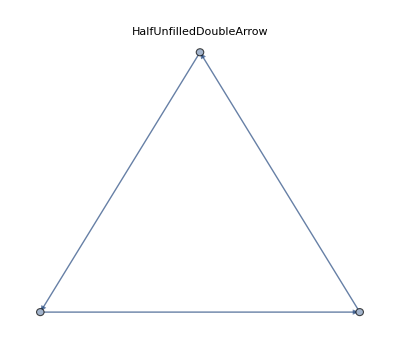
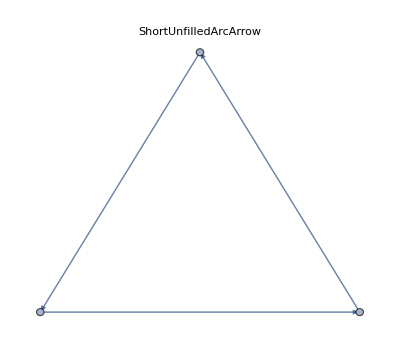
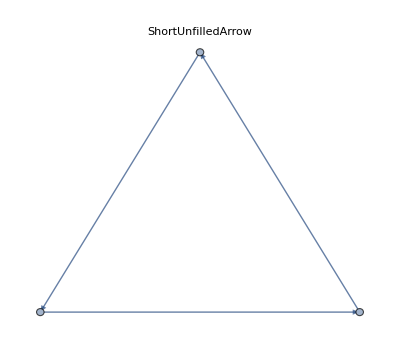
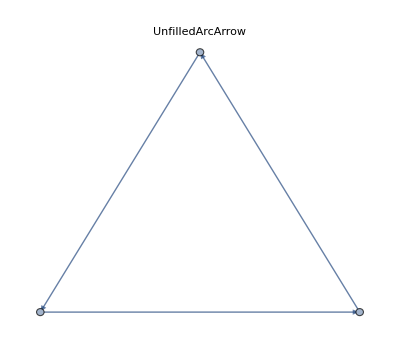
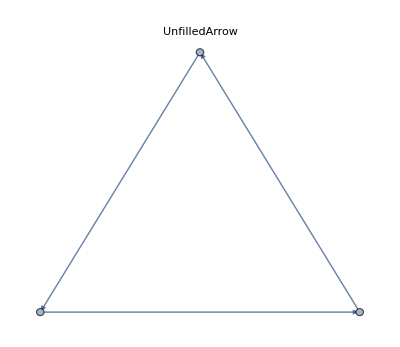

```mathematica
Table[Graph[{1->2,2->3,3->1},EdgeShapeFunction->{{kef,"ArrowSize"->0.1}},PlotLabel->Style[kef,10]],{kef,ResourceData["EdgeShapeFunction","UnfilledArrow"]}]
```

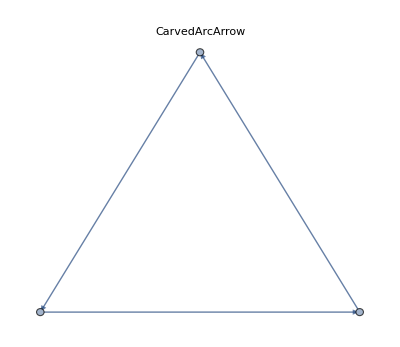
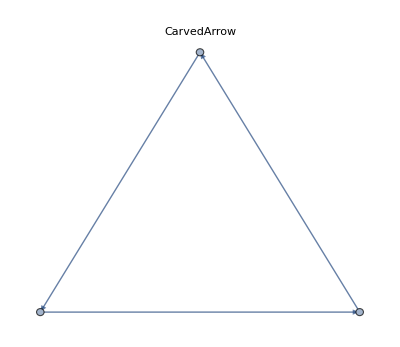
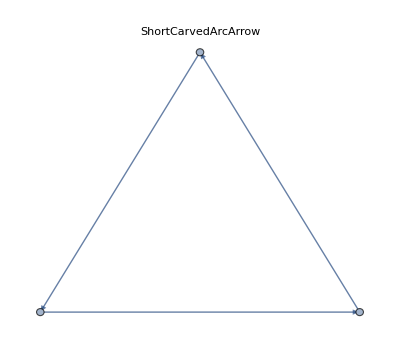
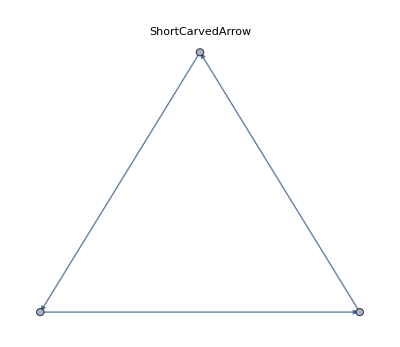

```mathematica
Table[Graph[{1->2,2->3,3->1},EdgeShapeFunction->{{kef,"ArrowSize"->0.1}},PlotLabel->Style[kef,10]],{kef,ResourceData["EdgeShapeFunction","CarvedArrow"]}]
```

Specify an edge function for an individual edge:

```mathematica
Graph[{1->2,2->3,3->1},EdgeShapeFunction->{1->2->"FilledArrow"}]
```

-Graphics-

Combine with a different default edge function:

```mathematica
Graph[{1->2,2->3,3->1},EdgeShapeFunction->{1->2->"FilledArrow","CarvedArrow"}]
```

-Graphics-

Draw edges by running a program:

```mathematica
ef[pts_List,e_]:=Block[{s=0.015,g=Graphics[Circle[]]},{Arrowheads[{{s,0.33,g},{s,0.67,g}}],Arrow[pts]}]
```

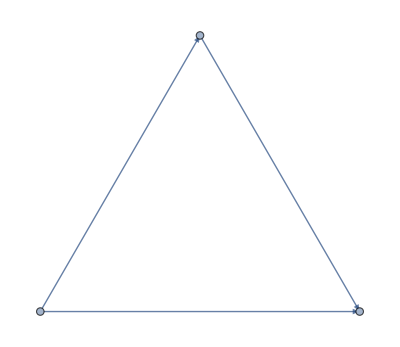

```mathematica
Graph[{1<->2,2<->3,3<->1},EdgeShapeFunction->ef]
```

EdgeShapeFunction can be combined with EdgeStyle:

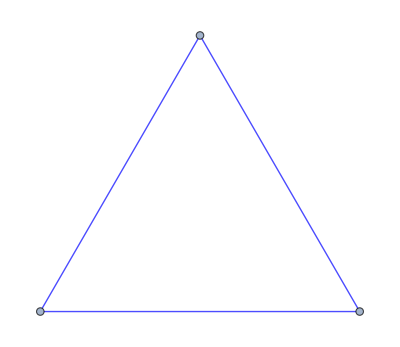

```mathematica
Graph[{1<->2,2<->3,3<->1},EdgeStyle->Blue,EdgeShapeFunction->(Line[#1]&)]
```

EdgeShapeFunction has higher priority than EdgeStyle:

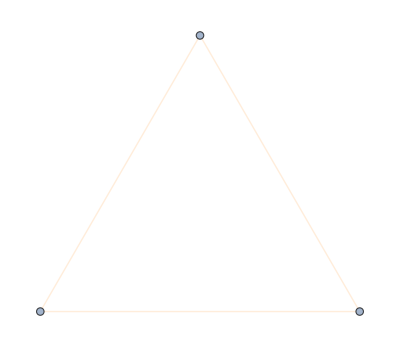

```mathematica
Graph[{1<->2,2<->3,3<->1},EdgeStyle->Blue,EdgeShapeFunction->({LightOrange,Line[#1]}&)]
```

### EdgeStyle

Style all edges:

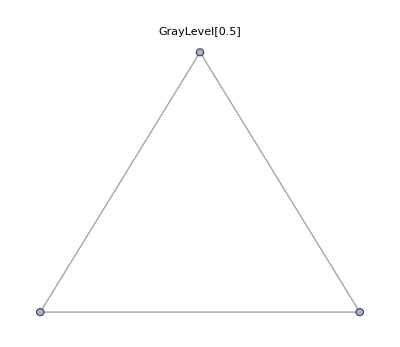
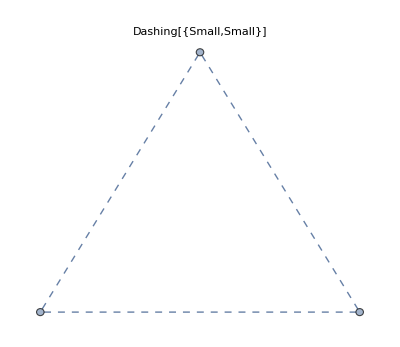
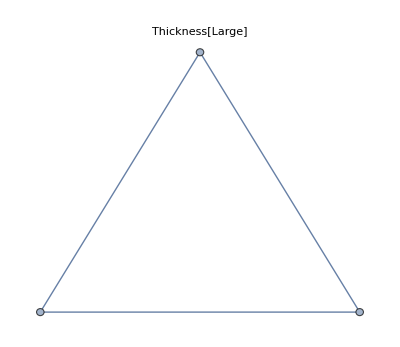

```mathematica
Table[Graph[{1<->2,2<->3,3<->1},EdgeStyle->style,PlotLabel->style],{style,{Gray,Dashed,Thick}}]
```

Style individual edges:

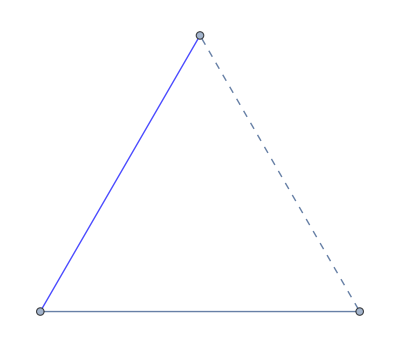

```mathematica
Graph[{1<->2,2<->3,3<->1},EdgeStyle->{1<->2->Blue,2<->3->Dashed}]
```

EdgeStyle can be combined with EdgeShapeFunction:

```mathematica
efA[el_,___]:=Arrow[el,0.1]
```

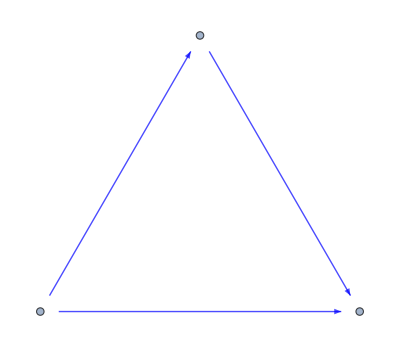

```mathematica
Graph[{1<->2,2<->3,3<->1},EdgeStyle->Blue,EdgeShapeFunction->efA]
```

EdgeShapeFunction has higher priority than EdgeStyle:

```mathematica
efB[el_,___]:={Red,Arrow[el,0.1]}
```

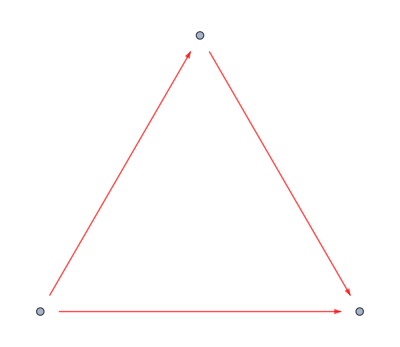

```mathematica
Graph[{1<->2,2<->3,3<->1},EdgeStyle->Blue,EdgeShapeFunction->efB]
```

EdgeStyle can be combined with BaseStyle:

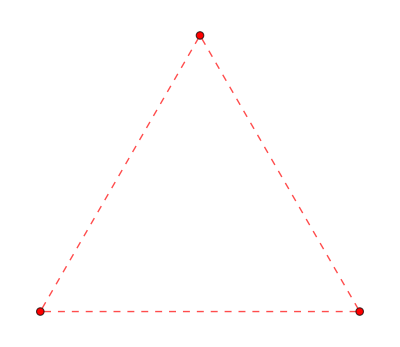

```mathematica
Graph[{1<->2,2<->3,3<->1},BaseStyle->Red,EdgeStyle->Dashed]
```

EdgeStyle has higher priority than BaseStyle:

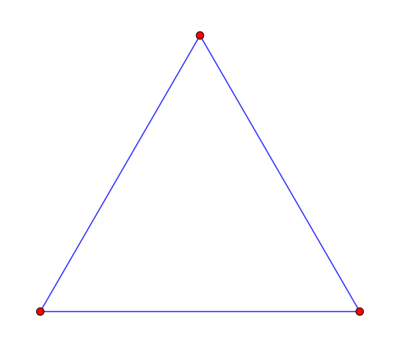

```mathematica
Graph[{1<->2,2<->3,3<->1},BaseStyle->Red,EdgeStyle->Blue]
```

### EdgeWeight

Specify a weight for all edges:

```mathematica
Graph[{1<->2,2<->3,3<->1},EdgeWeight->RandomInteger[5,3]]
```

-Graphics-

```mathematica
WeightedAdjacencyMatrix[Graph[{1<->2,2<->3,3<->1},EdgeWeight->RandomInteger[5,3]]]//MatrixForm
```

(0 | 3 | 5
3 | 0 | 3
5 | 3 | 0)

Use any numeric expression as a weight:

```mathematica
Graph[{1<->2,2<->3,3<->1},EdgeWeight->{a,b,c}]
```

-Graphics-

```mathematica
WeightedAdjacencyMatrix[Graph[{1<->2,2<->3,3<->1},EdgeWeight->{a,b,c}]]//MatrixForm
```

(0 | a | c
a | 0 | b
c | b | 0)

### GraphHighlight

Highlight the vertex 1:

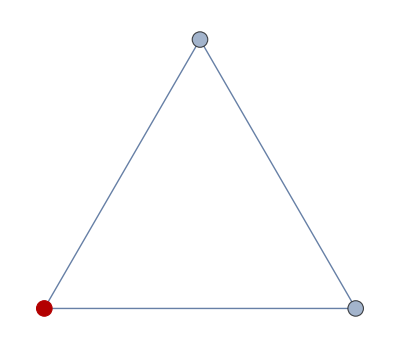

```mathematica
Graph[{1<->2,2<->3,3<->1},VertexSize->Tiny,GraphHighlight->{1}]
```

Highlight the edge 2<->3:

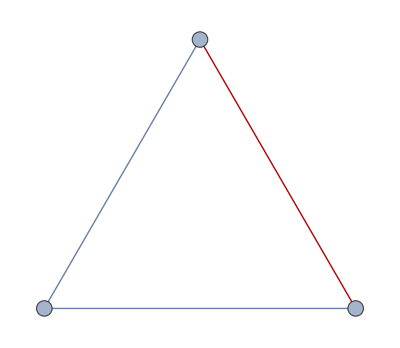

```mathematica
Graph[{1<->2,2<->3,3<->1},VertexSize->Tiny,GraphHighlight->{2<->3}]
```

Highlight vertices and edges:

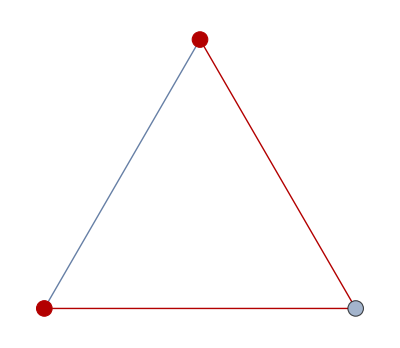

```mathematica
Graph[{1<->2,2<->3,3<->1},VertexSize->Tiny,GraphHighlight->{1,2,1<->3,2<->3}]
```

### GraphHighlightStyle

Get a list of built-in settings for GraphHighlightStyle:

```mathematica
ResourceData["GraphHighlightStyle"]
```

{Automatic,Dashed,Dotted,Thick,VertexConcaveDiamond,VertexDiamond,VertexTriangle,DehighlightFade,DehighlightGray,DehighlightHide}

Use built-in settings for GraphHighlightStyle:

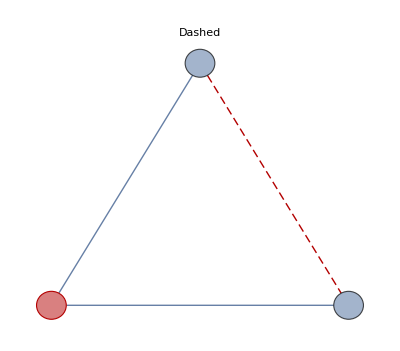
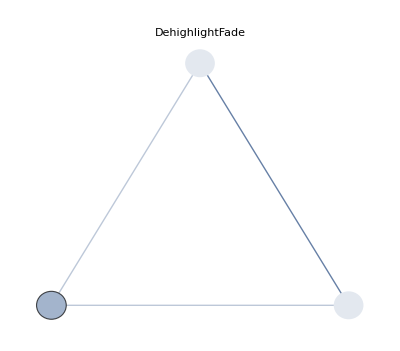
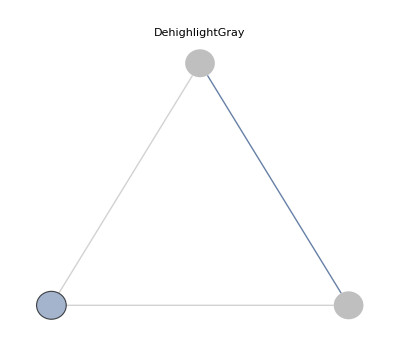
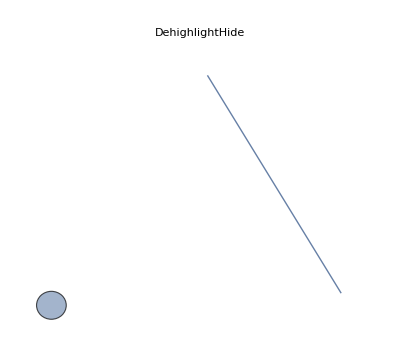
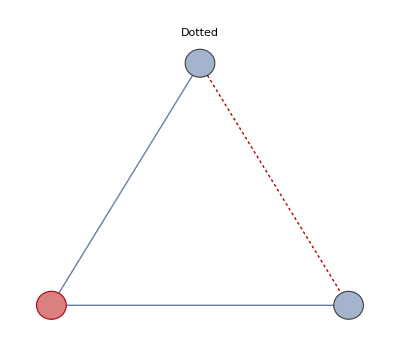
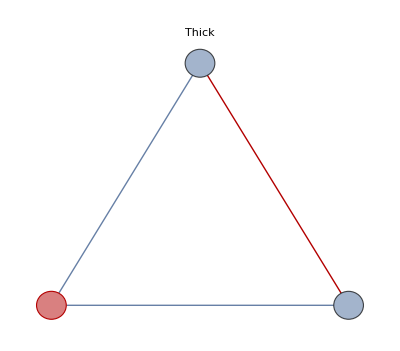
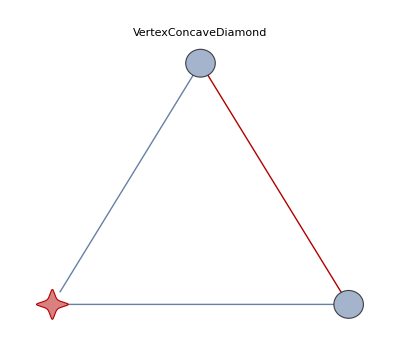
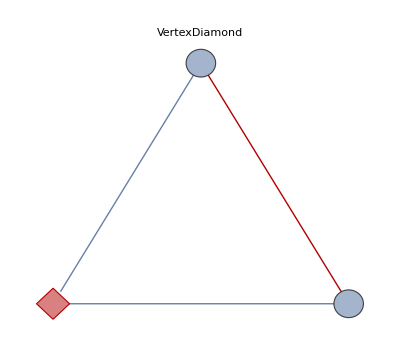

```mathematica
Graph[{1<->2,2<->3,3<->1},GraphHighlight->{1,2<->3},VertexSize->Small,GraphHighlightStyle->#,PlotLabel->#]&/@Complement[ResourceData["GraphHighlightStyle"],{Automatic}]
```

### GraphLayout

By default, the layout is chosen automatically:

```mathematica
Graph[{1<->2,2<->3,3<->1},GraphLayout->Automatic]
```

-Graphics-

Specify layouts on special curves:

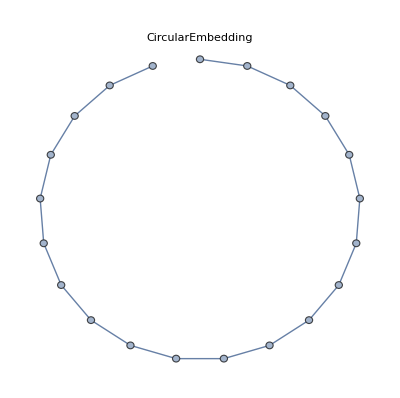
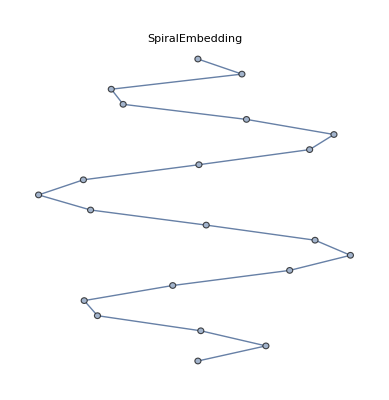

```mathematica
Table[Graph[Table[i<->i+1,{i,20}],GraphLayout->l,PlotLabel->l],{l,{"CircularEmbedding","SpiralEmbedding"}}]
```

Specify layouts that satisfy optimality criteria:

```mathematica
el=EdgeList@GridGraph[{10,10}];
```

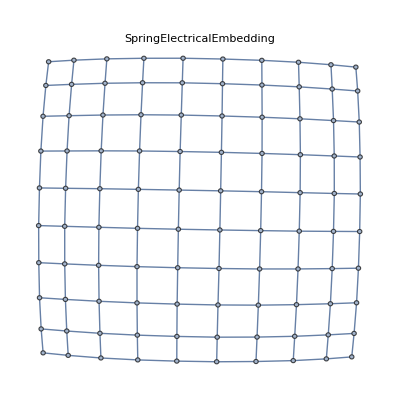
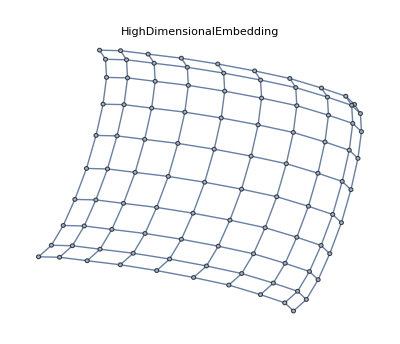
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Graph[el,GraphLayout->l,PlotLabel->Style[l,10]],{l,{"SpringElectricalEmbedding","SpringElectricalEmbedding","HighDimensionalEmbedding"}}]
```

VertexCoordinates overrides GraphLayout coordinates:

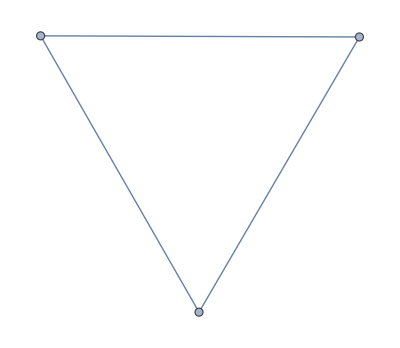
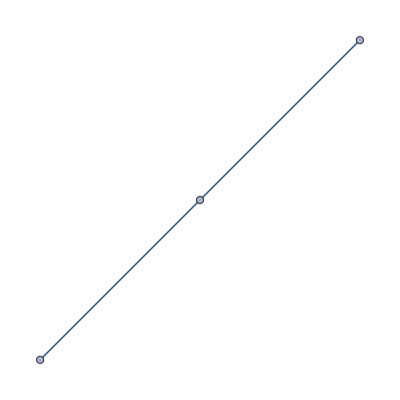

```mathematica
{Graph[{1<->2,2<->3,3<->1},GraphLayout->"SpringElectricalEmbedding"],Graph[{1<->2,2<->3,3<->1},GraphLayout->"SpringElectricalEmbedding",VertexCoordinates->Table[{i,i},{i,0,2}]]}
```

Use AbsoluteOptions to extract VertexCoordinates computed using a layout algorithm:

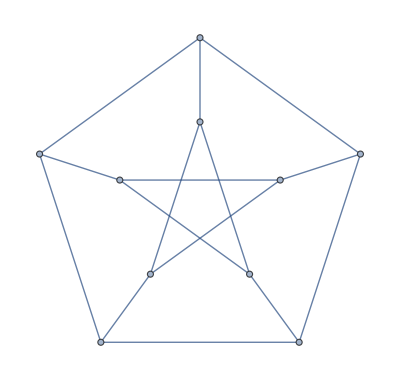

```mathematica
PetersenGraph[]
```

```mathematica
AbsoluteOptions[PetersenGraph[],VertexCoordinates]
```

{VertexCoordinates→{{0.951057,0.309017},{0.587785,-0.809017},{-0.587785,-0.809017},{-0.951057,0.309017},{-2.44929×10^-16,1.},{1.90211,0.618034},{1.17557,-1.61803},{-1.17557,-1.61803},{-1.90211,0.618034},{-4.89859×10^-16,2.}}}

### PlotTheme

#### BaseTheme

Use a common base theme:

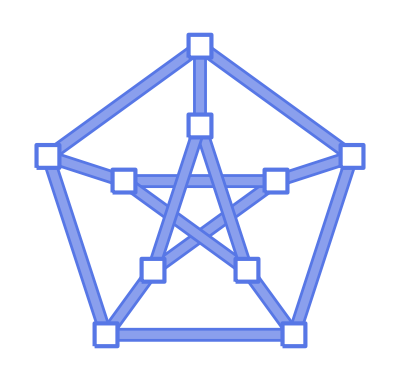

```mathematica
PetersenGraph[PlotTheme->"Business"]
```

Use a monochrome theme:

```mathematica
PetersenGraph[PlotTheme->"Monochrome"]
```

-Graphics-

#### FeatureThemes

Use a large graph theme:

```mathematica
PetersenGraph[PlotTheme->"LargeGraph"]
```

-Graphics-

Use a classic diagram theme:

```mathematica
PetersenGraph[PlotTheme->"ClassicDiagram"]
```

-Graphics-

### VertexCoordinates

By default, any vertex coordinates are computed automatically:

```mathematica
PetersenGraph[]
```

-Graphics-

Extract the resulting vertex coordinates using AbsoluteOptions:

```mathematica
AbsoluteOptions[PetersenGraph[],VertexCoordinates]
```

{VertexCoordinates→{{0.951057,0.309017},{0.587785,-0.809017},{-0.587785,-0.809017},{-0.951057,0.309017},{-2.44929×10^-16,1.},{1.90211,0.618034},{1.17557,-1.61803},{-1.17557,-1.61803},{-1.90211,0.618034},{-4.89859×10^-16,2.}}}

Specify a layout function along an ellipse:

```mathematica
ellipseLayout[n_,{a_,b_}]:=Table[{a Cos[2Pi/n u],b Sin[2Pi/n u]},{u,1,n}]
```

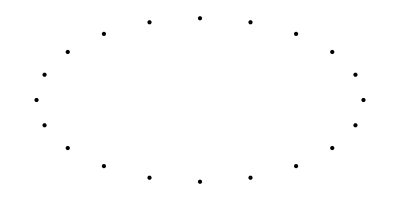

```mathematica
Graphics[Point[ellipseLayout[20,{2,1}]]]
```

Use it to generate vertex coordinates for a graph:

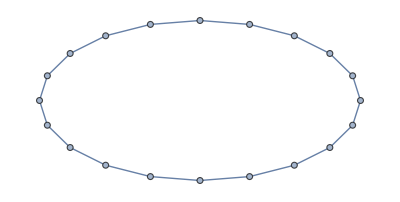

```mathematica
Graph[Table[i<->Mod[i+1,20,1],{i,20}],VertexCoordinates->ellipseLayout[20,{2,1}]]
```

VertexCoordinates has higher priority than GraphLayout:

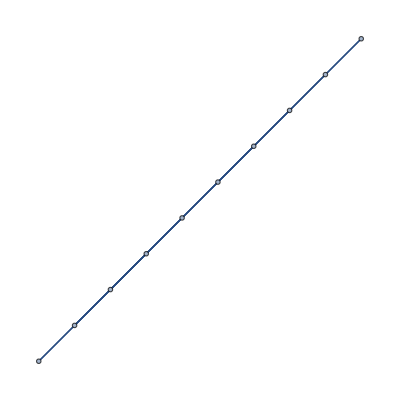

```mathematica
Graph[PetersenGraph[],VertexCoordinates->Table[{i,i},{i,10}],GraphLayout->"CircularEmbedding"]
```

### VertexLabels

Use vertex names as labels:

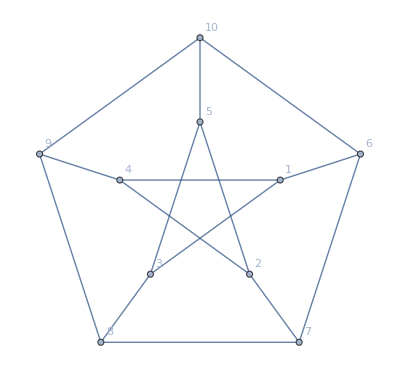

```mathematica
Graph[PetersenGraph[],VertexLabels->"Name"]
```

Label individual vertices:

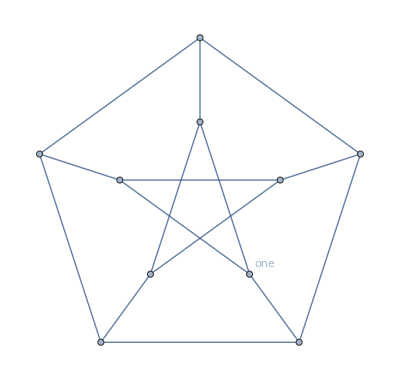

```mathematica
Graph[PetersenGraph[],VertexLabels->{2->"one"}]
```

Label all vertices:

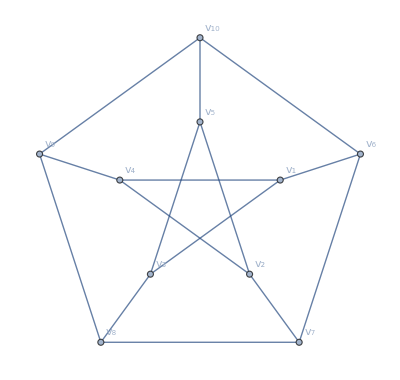

```mathematica
Graph[PetersenGraph[],VertexLabels->Table[i->Subscript[v, i],{i,10}]]
```

Use any expression as a label:

```mathematica
Graph[PetersenGraph[],VertexLabels->{1->-Graphics-,2->-Graphics-,3->-Graphics3D-},ImagePadding->30]
```

-Graphics-

Use Placed with symbolic locations to control label placement, including outside positions:

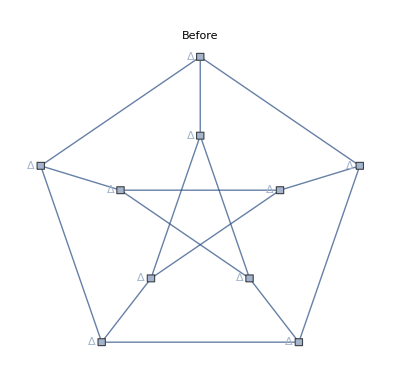
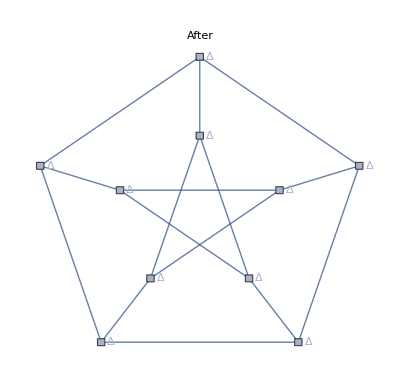
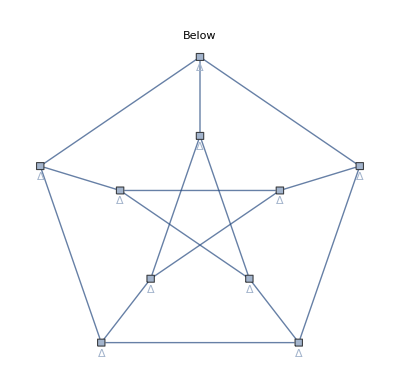
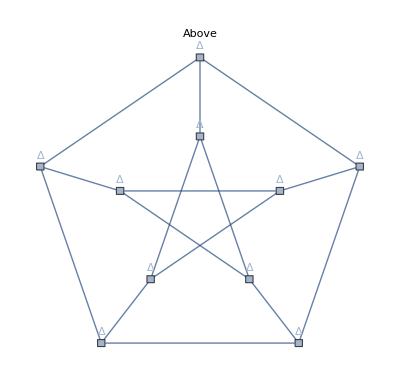

```mathematica
Table[PetersenGraph[VertexSize->0.1,VertexShapeFunction->"Square",VertexLabels->Table[ki->Placed["Δ",kp],{ki,10}],PlotLabel->kp],{kp,{Before,After,Below,Above}}]
```

Symbolic outside corner positions:

```mathematica
pl={{Before,Below},{After,Below},{Before,Above},{After,Above}};
```

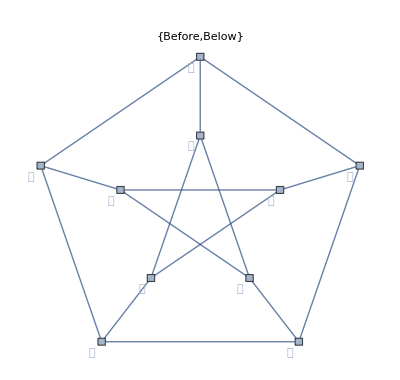
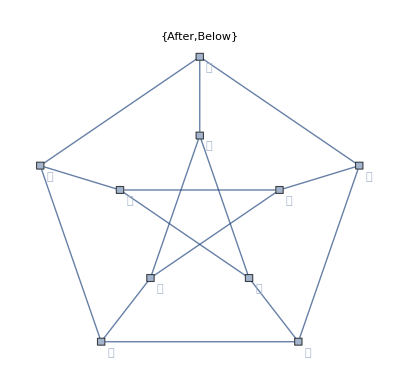
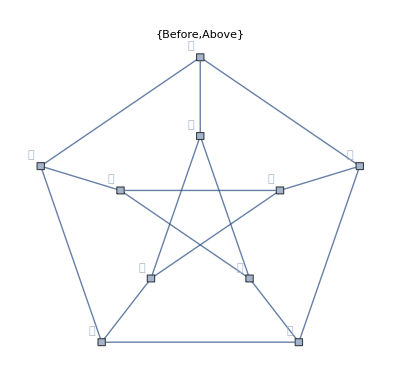
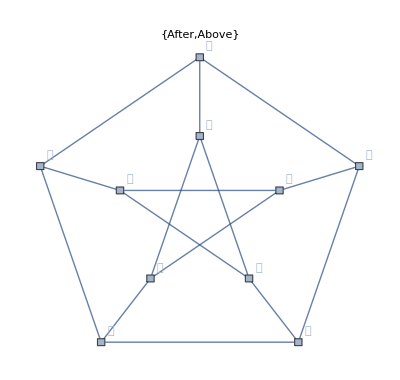

```mathematica
Table[PetersenGraph[VertexSize->0.1,VertexShapeFunction->"Square",VertexLabels->Table[ki->Placed["𝒢",kp],{ki,10}],PlotLabel->kp],{kp,pl}]
```

Symbolic inside positions:

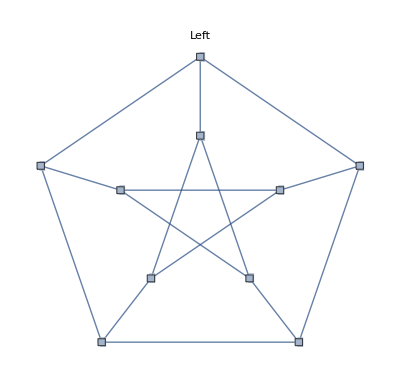
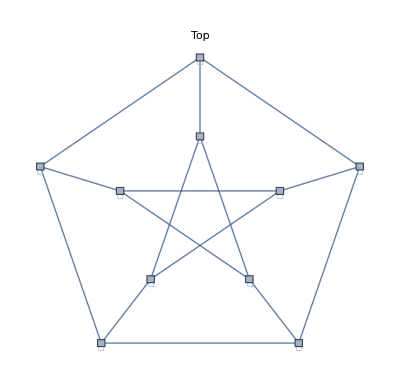
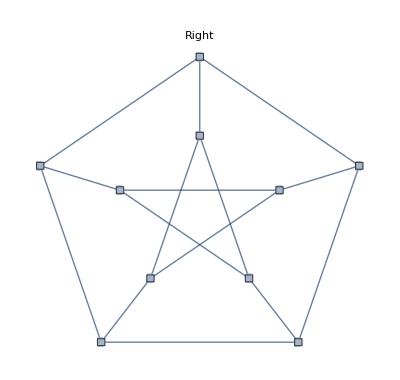
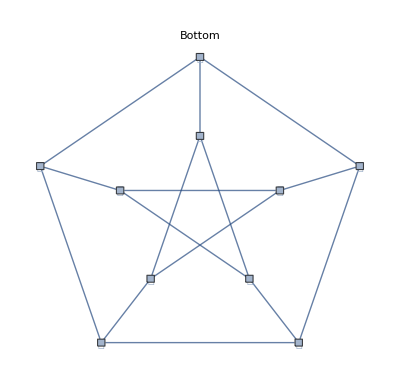

```mathematica
Table[PetersenGraph[VertexSize->0.1,VertexShapeFunction->"Square",VertexLabels->Table[ki->Placed["𝒢",kp],{ki,10}],PlotLabel->kp],{kp,{Left,Top,Right,Bottom}}]
```

Symbolic inside corner positions:

```mathematica
plInsideCorners={{Left,Bottom},{Right,Bottom},{Left,Top},{Right,Top}};
```

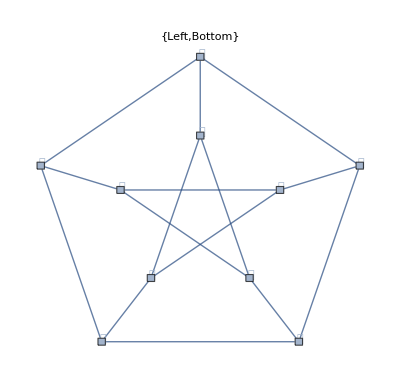
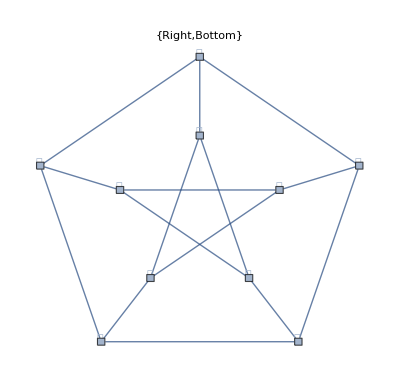
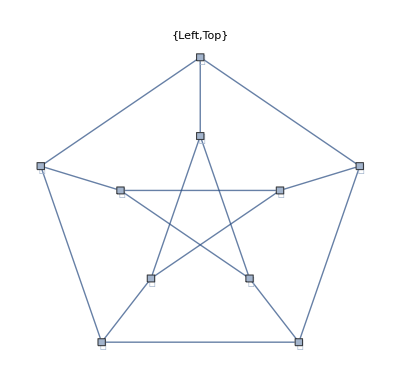
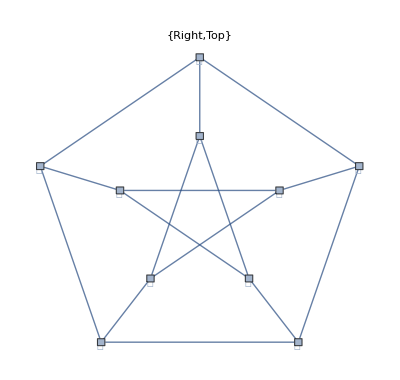

```mathematica
Table[PetersenGraph[VertexSize->0.1,VertexShapeFunction->"Square",VertexLabels->Table[ki->Placed["𝒢",kp],{ki,10}],PlotLabel->kp],{kp,plInsideCorners}]
```

Use explicit coordinates to place the center of labels:

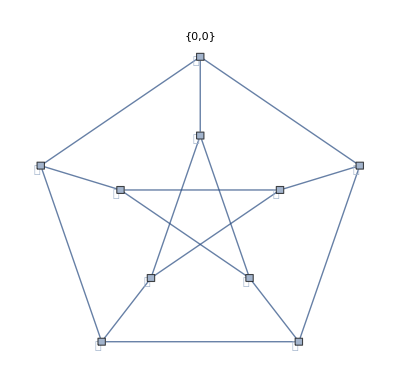
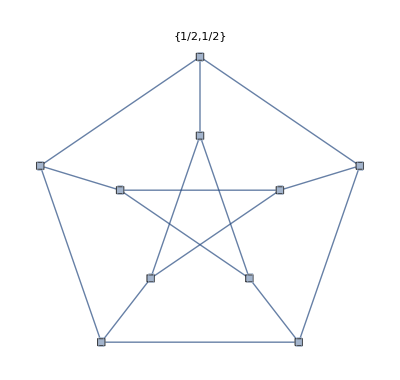
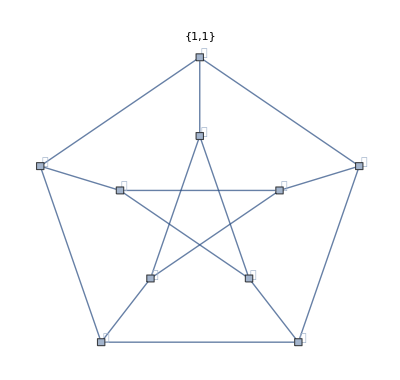

```mathematica
Table[PetersenGraph[VertexSize->0.1,VertexShapeFunction->"Square",VertexLabels->Table[ki->Placed["𝒢",kp],{ki,10}],PlotLabel->kp],{kp,{{0,0},{1/2,1/2},{1,1}}}]
```

Place all labels at the upper-right corner of the vertex and vary the coordinates within the label:

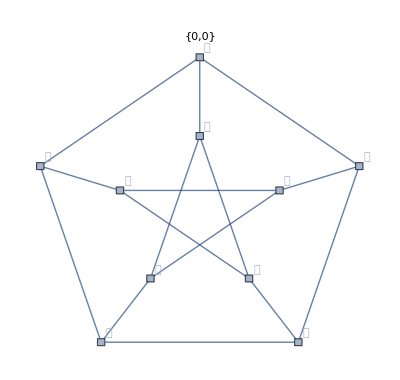
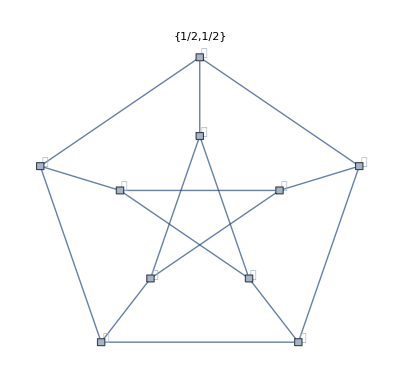
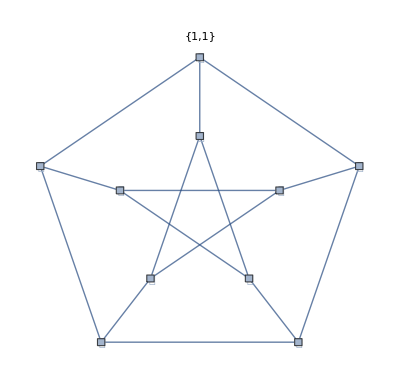

```mathematica
Table[PetersenGraph[VertexSize->0.1,VertexShapeFunction->"Square",VertexLabels->Table[ki->Placed["𝒢",{{1,1},kp}],{ki,10}],PlotLabel->kp],{kp,{{0,0},{1/2,1/2},{1,1}}}]
```

Place all labels at the center of vertices:

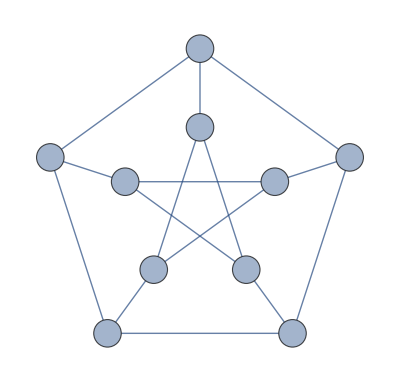

```mathematica
PetersenGraph[VertexSize->0.35,VertexLabels->Placed["𝒢",Center],VertexShapeFunction->"Circle"]
```

Place multiple labels using Place in a wrapper:

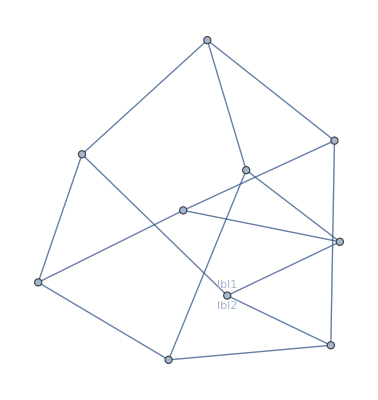

```mathematica
Graph[VertexList@PetersenGraph[]/.{3->Labeled[3,Placed[{"lbl1","lbl2"},{Above,Below}]]},EdgeList@PetersenGraph[]]
```

Place multiple labels using VertexLabels:

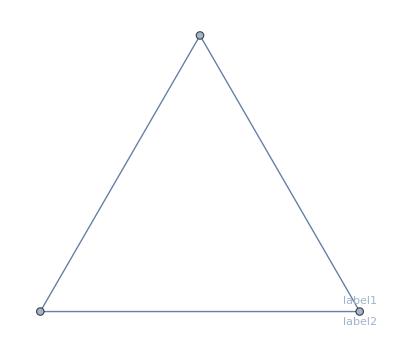

```mathematica
Graph[{1<->2,2<->3,3<->1},VertexLabels->{3->Placed[{"label1","label2"},{Above,Below}]}]
```

Use the argument to Placed to control formatting including Tooltip:

```mathematica
Graph[{1<->2,2<->3,3<->1},VertexLabels->Placed["Name",Tooltip]]
```

-Graphics-

Or StatusArea

```mathematica
Graph[{1<->2,2<->3,3<->1},VertexLabels->Placed["Name",StatusArea]]
```

-Graphics-

Use more elaborate formatting functions:

```mathematica
rotateLabel[label_]:=Rotate[label,45Degree]
```

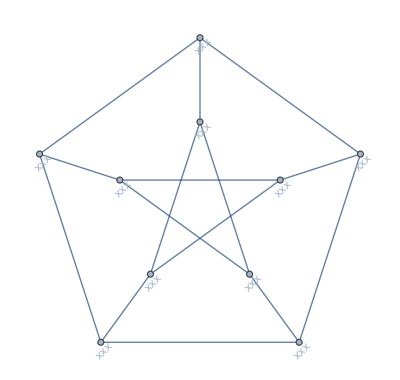

```mathematica
PetersenGraph[VertexLabels->Table[i->Placed["xxx",Below,rotateLabel],{i,10}]]
```

```mathematica
panelLabel[label_]:=Panel[label,FrameMargins->0,Background->Lighter[Yellow,0.7]]
```

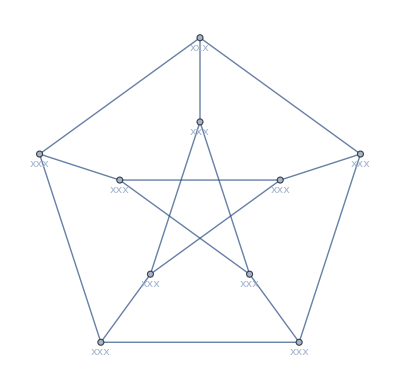

```mathematica
PetersenGraph[VertexLabels->Table[i->Placed["xxx",Below,panelLabel],{i,10}]]
```

```mathematica
hyperlinkLabel[label_]:=Hyperlink[label,"https://en.wikipedia.org/wiki/Petersen_graph"]
```

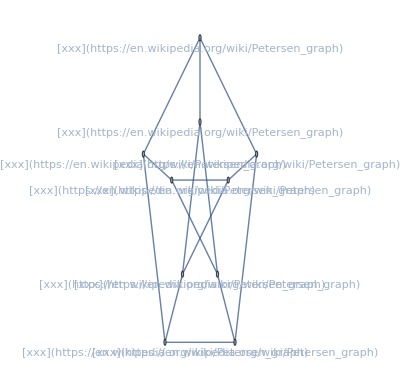

```mathematica
PetersenGraph[VertexLabels->Table[i->Placed["xxx",Below,hyperlinkLabel],{i,10}]]
```

### VertexShape

Use any Graphics, Image, or Graphics3D as a vertex shape:

```mathematica
graphics={Graphics[{LightBlue,RegularPolygon[5]},ImageSize->50],ImageResize[CurrentScreenImage[],{50}],Graphics3D[Torus[],ImageSize->50]}
```

{-Graphics-,-Graphics-,-Graphics3D-}

```mathematica
Table[{PetersenGraph[VertexShape->s,VertexSize->Medium,ImageSize->Medium]},{s,graphics}]
```

{{-Graphics-},{-Graphics-},{-Graphics-}}

Specify vertex shapes for individual vertices:

```mathematica
PetersenGraph[VertexShape->{2->ArrayPlot[RandomInteger[10,{200,200}],ImageSize->50]},VertexSize->Medium]
```

-Graphics-

VertexShape can be combined with VertexSize:

```mathematica
Table[PetersenGraph[VertexSize->s,VertexShape->-Graphics-,PlotLabel->s],{s,{Small,Large}}]
```

{-Graphics-,-Graphics-}

VertexShape is not affected by VertexStyle:

```mathematica
PetersenGraph[VertexSize->0.2,VertexShape->-Graphics-,VertexStyle->Blue]
```

-Graphics-

VertexShapeFunction has higher priority than VertexShape:

```mathematica
PetersenGraph[VertexSize->0.1,VertexShapeFunction->"Square",VertexShape->-Graphics-]
```

-Graphics-

### VertexShapeFunction

Get a list of built-in collections for VertexShapeFunction:

```mathematica
ResourceData["VertexShapeFunction"]
```

{Capsule,Circle,ConcaveDiamond,ConcaveHexagon,ConcavePentagon,ConcaveSquare,ConcaveTriangle,Diamond,DownTrapezoid,FiveDown,Hexagon,Octagon,Parallelogram,Pentagon,Point,Rectangle,RoundedDiamond,RoundedDownTrapezoid,RoundedFiveDown,RoundedHexagon,RoundedParallelogram,RoundedPentagon,RoundedRectangle,RoundedSquare,RoundedTriangle,RoundedUpTrapezoid,Square,Star,Triangle,UpTrapezoid}

Use built-in settings for VertexShapeFunction in the “Basic” collection:

```mathematica
ResourceData["VertexShapeFunction","Basic"]
```

{Capsule,Circle,Diamond,DownTrapezoid,FiveDown,Hexagon,Octagon,Parallelogram,Pentagon,Point,Rectangle,Square,Star,Triangle,UpTrapezoid}

Simple basic shapes:

```mathematica
Table[PetersenGraph[VertexShapeFunction->vf,VertexSize->0.2,PlotLabel->vf],{vf,{"Triangle","Square","Rectangle","Pentagon","Hexagon","Octagon"}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Common basic shapes:

```mathematica
Table[PetersenGraph[VertexShapeFunction->vf,VertexSize->0.2,PlotLabel->vf],{vf,{"DownTrapezoid","UpTrapezoid","Parallelogram","FiveDown","Circle","Diamond","Star","Capsule"}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Use built-in settings for VertexShapeFunction in the “Rounded” collection:

```mathematica
ResourceData["VertexShapeFunction","Rounded"]
```

{RoundedDiamond,RoundedDownTrapezoid,RoundedFiveDown,RoundedHexagon,RoundedParallelogram,RoundedPentagon,RoundedRectangle,RoundedSquare,RoundedTriangle,RoundedUpTrapezoid}

```mathematica
Table[PetersenGraph[VertexShapeFunction->vf,VertexSize->0.2,PlotLabel->vf],{vf,{"RoundedDiamond","RoundedDownTrapezoid","RoundedFiveDown","RoundedHexagon","RoundedParallelogram","RoundedPentagon","RoundedRectangle","RoundedSquare","RoundedTriangle","RoundedUpTrapezoid"}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Use built-in settings for VertexShapeFunction in the “Concave” collection:

```mathematica
ResourceData["VertexShapeFunction","Concave"]
```

{ConcaveDiamond,ConcaveHexagon,ConcavePentagon,ConcaveSquare,ConcaveTriangle}

```mathematica
Table[PetersenGraph[VertexShapeFunction->vf,VertexSize->0.2,PlotLabel->vf],{vf,ResourceData["VertexShapeFunction","Concave"]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Draw individual vertices:

```mathematica
PetersenGraph[VertexShapeFunction->{1->"Diamond"},VertexSize->0.2]
```

-Graphics-

Combine with a default vertex function:

```mathematica
PetersenGraph[VertexShapeFunction->{1->"Diamond","Triangle"},VertexSize->0.2]
```

-Graphics-

Draw vertices using a predefined graphic:

```mathematica
PetersenGraph[VertexShapeFunction->(Inset[-Graphics-,#]&)]
```

-Graphics-

Draw vertices by running a program:

```mathematica
vg[{xc_,yc_},name_,{w_,h_}]:=Block[{xmin=xc-w,xmax=xc+w,ymin=yc-h,ymax=yc+h},Polygon[{{xmin,ymin},{xmax,ymax},{xmin,ymax},{xmax,ymin}}]];
```

```mathematica
PetersenGraph[VertexShapeFunction->vg,VertexSize->0.2]
```

-Graphics-

VertexShapeFunction can be combined with VertexStyle:

```mathematica
vgA[{xc_,yc_},name_,{w_,h_}]:=Rectangle[{xc-w,yc-h},{xc+w,yc+h}]
```

```mathematica
PetersenGraph[VertexSize->0.2,VertexStyle->LightOrange,VertexShapeFunction->vgA]
```

-Graphics-

VertexShapeFunction has higher priority than VertexStyle:

```mathematica
vfB[{xc_,yc_},name_,{w_,h_}]:={LightPurple,Rectangle[{xc-w,yc-h},{xc+w,yc+h}]}
```

```mathematica
PetersenGraph[VertexSize->0.2,VertexStyle->LightYellow,VertexShapeFunction->vfB]
```

-Graphics-

VertexShapeFunction can be combined with VertexSize:

```mathematica
PetersenGraph[VertexShapeFunction->"Star",VertexSize->{1->Small,Medium}]
```

-Graphics-

VertexShapeFunction has higher priority than VertexShape:

```mathematica
PetersenGraph[VertexSize->0.3,VertexShapeFunction->"Star",VertexShape->-Graphics-]
```

-Graphics-

### VertexSize

By default, the size of vertices is computed automatically:

```mathematica
PetersenGraph[VertexSize->Automatic]
```

-Graphics-

Specify the size of all vertices using symbolic vertex size:

```mathematica
Table[PetersenGraph[VertexSize->ks,PlotLabel->ks],{ks,{Tiny,Small,Medium,Large}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Use a fraction of the minimum distance between vertex coordinates:

```mathematica
Table[PetersenGraph[VertexSize->ks,PlotLabel->ks],{ks,0.1,1,0.3}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Use a fraction of the overall diagonal for all vertex coordinates:

```mathematica
Table[PetersenGraph[VertexSize->{"Scaled",ks},PlotLabel->{"Scaled",ks}],{ks,0.1,1,0.3}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Specify size in both the x and y directions:

```mathematica
Table[PetersenGraph[VertexSize->ks,PlotLabel->ks],{ks,{{0.1,0.2},{0.2,0.1}}}]
```

{-Graphics-,-Graphics-}

Specify the size for individual vertices:

```mathematica
PetersenGraph[VertexSize->{1->0.2,2->0.3}]
```

-Graphics-

VertexSize can be combined with VertexShapeFunction:

```mathematica
Table[PetersenGraph[VertexSize->ks,VertexShapeFunction->"Square",PlotLabel->ks],{ks,{0.05,0.1,0.2}}]
```

{-Graphics-,-Graphics-,-Graphics-}

VertexSize can be combined with VertexShape:

```mathematica
Table[PetersenGraph[VertexSize->ks,VertexShape->-Graphics-,PlotLabel->ks],{ks,{0.1,0.2,0.4}}]
```

{-Graphics-,-Graphics-,-Graphics-}

### VertexStyle

Style all vertices:

```mathematica
Table[PetersenGraph[VertexStyle->kstyle,VertexSize->0.2],{kstyle,{Yellow,EdgeForm[Dashed]}}]
```

{-Graphics-,-Graphics-}

Style individual vertices:

```mathematica
PetersenGraph[VertexStyle->{1->Blue,2->LightRed},VertexSize->0.2]
```

-Graphics-

VertexShapeFunction can be combined with VertexStyle:

```mathematica
vfA[{xc_,yc_},name_,{w_,h_}]:=Rectangle[{xc-w,yc-h},{xc+w,yc+h}]
```

```mathematica
PetersenGraph[VertexSize->0.2,VertexStyle->Blue,VertexShapeFunction->vfA]
```

-Graphics-

VertexShapeFunction higher priority than VertexStyle:

```mathematica
vfB[{xc_,yc_},name_,{w_,h_}]:={LightGreen,Rectangle[{xc-w,yc-h},{xc+w,yc+h}]}
```

```mathematica
PetersenGraph[VertexSize->0.2,VertexStyle->LightPurple,VertexShapeFunction->vfB]
```

-Graphics-

VertexStyle can be combined with BaseStyle:

```mathematica
PetersenGraph[VertexStyle->LightBlue,BaseStyle->EdgeForm[Dotted],VertexSize->0.2]
```

-Graphics-

VertexStyle has higher priority than BaseStyle:

```mathematica
PetersenGraph[VertexStyle->Red,BaseStyle->Gray,VertexSize->0.2]
```

-Graphics-

### VertexWeight

Set the weight for all vertices:

```mathematica
PetersenGraph[VertexWeight->RandomReal[{2,5},10]]
```

-Graphics-

```mathematica
AnnotationValue[{PetersenGraph[VertexWeight->RandomReal[{2,5},10]],1},VertexWeight]
```

3.30211

Use any numeric expression as a weight:

```mathematica
PetersenGraph[VertexWeight->{a,b,c,d,e,f,g,h,i,j}]
```

-Graphics-

```mathematica
AnnotationValue[{PetersenGraph[VertexWeight->{a,b,c,d,e,f,g,h,i,j}],1},VertexWeight]
```

a

## Applications

Generate a network of “nearby” words in a dictionary:

```mathematica
words=DictionaryLookup["wol*"]
```

{wold,wolds,wolf,wolfed,wolfhound,wolfhounds,wolfing,wolfish,wolfishly,wolfram,wolfs,wolverine,wolverines,wolves}

```mathematica
Flatten[Map[(Thread[#->DeleteCases[Nearest[words,#,3],#]])&,words]]
```

{wold->wolds,wold->wolf,wolds->wold,wolds->wolfs,wolf->wold,wolf->wolfs,wolfed->wold,wolfed->wolf,wolfhound->wolfhounds,wolfhound->wolfed,wolfhounds->wolfhound,wolfhounds->wolds,wolfing->wolfish,wolfing->wolf,wolfish->wolfing,wolfish->wolfishly,wolfishly->wolfish,wolfishly->wolfing,wolfram->wolf,wolfram->wolfed,wolfs->wolds,wolfs->wolf,wolverine->wolverines,wolverine->wolfing,wolverines->wolverine,wolverines->wolves,wolves->wolds,wolves->wolfed}

```mathematica
Graph[Flatten[Map[(Thread[#->DeleteCases[Nearest[words,#,3],#]])&,words]],VertexLabels->"Name",ImageSize->450]
```

-Graphics-

## Possible Issues

Parallel edges are undistinguishable in Graph:

```mathematica
Graph[Flatten[EdgeList[PetersenGraph[]]/.{1<->4->{Style[1<->4,Red],Style[1<->4,Blue]}}]]
```

-Graphics-

Use EdgeTaggedGraph to assign a unique tag to each edge:

```mathematica
EdgeTaggedGraph[Flatten[EdgeList[PetersenGraph[]]/.{1<->4->{Style[1<->4,Red],Style[1<->4,Blue]}}]]
```

-Graphics-

```mathematica
EdgeList[EdgeTaggedGraph[Flatten[EdgeList[PetersenGraph[]]/.{1<->4->{Style[1<->4,Red],Style[1<->4,Blue]}}]]]
```

{131,141,142,161,241,251,271,351,381,491,5101,671,6101,781,891,9101}

## UndirectedEdge

## Basic Examples

Build a graph with undirected edges:

```mathematica
Graph[{UndirectedEdge[a,b],UndirectedEdge[b,c],UndirectedEdge[c,a]}]
```

-Graphics-

List of edges:

```mathematica
EdgeList[Graph[{UndirectedEdge[a,b],UndirectedEdge[b,c],UndirectedEdge[c,a]}]]
```

{a<->b,b<->c,c<->a}

Use EscueEsc to enter <-> directly:

```mathematica
Graph[{a<->b,b<->c,c<->a,c<->d,b<->e}]
```

-Graphics-

Enter using a two-way rule <->:

```mathematica
Graph[{a<->b,b<->c,c<->a,a<->d,b<->e,c<->f}]
```

-Graphics-

The two-way rules are converted to undirected edges:

```mathematica
EdgeList[Graph[{a<->b,b<->c,c<->a,a<->d,b<->e,c<->f}]]
```

{a<->b,b<->c,c<->a,a<->d,b<->e,c<->f}

Style and label individual edges:

```mathematica
Graph[{Style[a<->b,Red],Style[b<->c,Dashed],Labeled[c<->a,"hello"]}]
```

-Graphics-

StandardForm formatting:

```mathematica
UndirectedEdge[a,b]
```

a<->b

```mathematica
UndirectedEdge[a,b,t]
```

abt

### Properties and Relations

Use UndirectedEdge to construct undirected graphs:

```mathematica
EdgeList[PetersenGraph[]]
```

{1<->3,1<->4,1<->6,2<->4,2<->5,2<->7,3<->5,3<->8,4<->9,5<->10,6<->7,6<->10,7<->8,8<->9,9<->10}

```mathematica
Graph[{1<->3,1<->4,1<->6,2<->4,2<->5,2<->7,3<->5,3<->8,4<->9,5<->10,6<->7,6<->10,7<->8,8<->9,9<->10}]
```

-Graphics-

Tree graphs:

```mathematica
TreeGraph[{1<->2,1<->3,1<->4}]
```

-Graphics-

PathGraphs:

```mathematica
PathGraph[{1<->2,2<->3,3<->4}]
```

-Graphics-

The adjacency matrix of an undirected graph is symmetric:

```mathematica
PetersenGraph[]
```

-Graphics-

```mathematica
AdjacencyMatrix[PetersenGraph[]]//MatrixForm
```

(0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0)

## DirectedEdge

Build a graph with directed edges:

```mathematica
Graph[{DirectedEdge[a,b],DirectedEdge[b,c],DirectedEdge[c,a]}]
```

-Graphics-

List of edges:

```mathematica
EdgeList[Graph[{DirectedEdge[a,b],DirectedEdge[b,c],DirectedEdge[c,a]}]]
```

{a->b,b->c,c->a}

Use EscdeEsc to enter -> directly:

```mathematica
Graph[EdgeList[PetersenGraph[]]/.{1<->4->a->b}]
```

-Graphics-

```mathematica
EdgeList[Graph[EdgeList[PetersenGraph[]]/.{1<->4->a->b}]]
```

{1<->3,a->b,1<->6,2<->4,2<->5,2<->7,3<->5,3<->8,4<->9,5<->10,6<->7,6<->10,7<->8,8<->9,9<->10}

Style and label individual edges:

```mathematica
Graph[{Style[a->b,LightRed],Style[b->c,Dashed],Labeled[c->a,"hello"]}]
```

-Graphics-

StandardForm formatting

```mathematica
DirectedEdge[a,b]
```

a->b

```mathematica
DirectedEdge[a,b,t]
```

abt

## Properties & Relations

Use DirectedEdge to construct directed graphs:

```mathematica
Graph[{a->b,b->c,c->a}]
```

-Graphics-

Tree graphs:

```mathematica
TreeGraph[{1->2,1->3,1->4}]
```

-Graphics-

PathGraphs:

```mathematica
PathGraph[{1->2,2->3,3->4}]
```

-Graphics-

Inside graph constructors, Rule[a,b] is converted to DirectedEdge[a,b]:

```mathematica
Graph[{a->b,a->c,a->d}]
```

-Graphics-

The adjacency matrix of a directed graph can be unsymmetric:

```mathematica
Graph[{1->2,2->3,3->1}]
```

-Graphics-

```mathematica
AdjacencyMatrix[Graph[{1->2,2->3,3->1}]]//MatrixForm
```

(0 | 1 | 0
0 | 0 | 1
1 | 0 | 0)